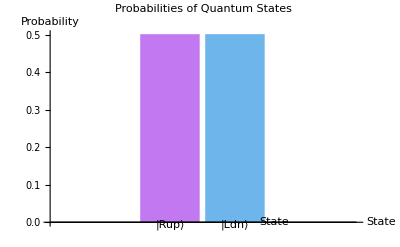

```mathematica
(*Representing the quantum states|R_up>and|L_dn>*)
Rup={1,0}; (* |R_up>state*)
Ldn={0,1}; (* |L_dn>state*)

(*Define α and β as symbolic variables*)
α=Symbol["α"];
β=-α; (*Since β=-α as per your definition*)

(*Normalization condition:Abs[α]^2+Abs[β]^2=1*)
NormalizeCondition=Abs[α]^2+Abs[β]^2==1;

(*Solve for α under the normalization condition*)
solutions=Solve[NormalizeCondition,α,Reals];

(*Choose the first solution for α and calculate β=-α*)
αNorm=α/. solutions[[1]];
βNorm=-αNorm;

(*Define the final quantum state function psi[f] with normalized α and β*)
psi[f_]:=αNorm*Rup-βNorm*Ldn;

(*Probabilities for measuring|R_up>and|L_dn>states*)
probUp=Abs[psi[f][[1]]]^2; (*Probability of|R_up>*)
probDn=Abs[psi[f][[2]]]^2; (*Probability of|L_dn>*)

(*Plotting the probabilities with a bar chart*)
BarChart[{probUp,probDn},ChartLabels->{"|Rup⟩","|Ldn⟩"},ChartStyle->"Pastel",AxesLabel->{"State","Probability"},PlotLabel->"Probabilities of Quantum States"]
```